# Elliptical Constraint Algorithm

All I need are to build the constraint matrix B and make sure the simplified TRS sub-problem algorithm is correct.

### Test Suite

Most journals would like a test on some standard test-set.  I do development on random problems because it is easier.

I did a search for bound constrained quadratic program test set and found the stack exchange page 
https://or.stackexchange.com/questions/79/where-can-i-find-test-instances-for-convex-quadratic-programming
and some links 
https://qplib.zib.de/index.html
and
https://www.minlplib.org/instances.html
and
https://www.alglib.net/optimization/quadraticprogramming.php
and
https://www.sciencedirect.com/science/article/pii/S0045794996001733

### Build B Algorithm

Pretty simple.  Compute distances to edges.  Find distances.  Put on diagonal.

```mathematica
Clear[BMat, ConsQuad]
BMat[{l_,u_}][c_]:=Module[{rs},
rs=Map[Min,{c-l,u-c}ᵀ];
DiagonalMatrix[rs]
]
e[i_,2]:= SparseArray[{i->1.0},2];
ConsQuad[{M_,c_}][x_]:= (x-c).MatrixPower[M,-2].(x-c)
```

Testing

```mathematica
{l,u}={{1,3},{4,9}};
c={1.9,5.5};
M=BMat[{l,u}][c];
TabView[{
"Diagram"->Graphics[{
{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
{LightPink, EdgeForm[Red], Disk[c,Diagonal[M]]},
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c]}
},
AspectRatio->1,
Frame->True
],
"Contours"->ContourPlot[
ConsQuad[{M,c}][{x1,x2}],
{x1, l⟦1⟧,u⟦1⟧},{x2, l⟦2⟧,u⟦2⟧},
ContourLabels->All,
Prolog->{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
Epilog->{
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c],Circle[c,Diagonal[M]]}},
AspectRatio->1,
PlotRange->{0,1}]
}]
```

12

```mathematica
{l,u}={{1,3},{4,9}};
c={2.9,5.5};
M=BMat[{l,u}][c];
TabView[{
"Diagram"->Graphics[{
{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
{LightPink, EdgeForm[Red], Disk[c,Diagonal[M]]},
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c]}
},
AspectRatio->1,
Frame->True
],
"Contours"->ContourPlot[
ConsQuad[{M,c}][{x1,x2}],
{x1, l⟦1⟧,u⟦1⟧},{x2, l⟦2⟧,u⟦2⟧},
ContourLabels->All,
Prolog->{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
Epilog->{
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c],Circle[c,Diagonal[M]]}},
AspectRatio->1,
PlotRange->{0,1}]
}]
```

12

```mathematica
{l,u}={{1,3},{4,9}};
c={1.2,5.5};
M=BMat[{l,u}][c];
TabView[{
"Diagram"->Graphics[{
{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
{LightPink, EdgeForm[Red], Disk[c,Diagonal[M]]},
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c]}
},
AspectRatio->1,
Frame->True
],
"Contours"->ContourPlot[
ConsQuad[{M,c}][{x1,x2}],
{x1, l⟦1⟧,u⟦1⟧},{x2, l⟦2⟧,u⟦2⟧},
ContourLabels->All,
Prolog->{LightGreen,EdgeForm[Blue],Rectangle[l,u]},
Epilog->{
{Green, Table[
Line[{c-M⟦i,i⟧e[i,2],c+M⟦i,i⟧e[i,2]}],
{i,2}]},
{Red, PointSize[0.02],Point[c],Circle[c,Diagonal[M]]}},
AspectRatio->1,
PlotRange->{0,1}]
}]
```

12

The trust region version adds in a background distance Δ in all the remaining directions.  This is to be added later. It is NOT needed for our current quadratic program problem.

### TRS Eigenvalue Algorithm

An eigenvalue based algorithm for the trust region sub-problem
	argmin_(√(p.B.p)≤Δ)(g.p+0.5p.A.p)
described in the reference is defined below.  There are other versions that might be more suitable.

Adachi, S., Iwata, S., Nakatsukasa, Y., & Takeda, A.
Solving the trust-region subproblem by a generalized eigenvalue problem.
SIAM Journal on Optimization 27.1 (2017): 269-291.

```mathematica
Adachi[{A_,g_},{B_,Δ_}]:= Module[
{M0, M1,λMin,y1y2Min,y1Min,y2Min},
{M0,M1}=Map[ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),-({{0, B}, {B, 0}})}];
(* Eigensystem sorts by |λ|  *)
{λMin,y1y2Min}=Sort[Eigensystem[{M0,M1}]ᵀ]⟦-1⟧;
{y1Min,y2Min}=Partition[y1y2Min,Length[g]];
Chop[-Sign[g.y2Min]Δ y1Min/(√(y1Min.B.y1Min))]
]
```

Testing. Not surprisingly the Adachi Algorithm is better than the built-in numerical routine.  It always satisfies the constraint to double precision accuracy and always has a lower reported minimum.

```mathematica
n=12;
{A,B}=RandomReal[{-1,1},{2,n,n}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},n];
Δ=0.1;
f[x_]:=0.5x.A.x+g.x
xVar=Array[x,{n}];
x0=RandomReal[{-1,1},n];
{FMinVal, FMinSub}=FindMinimum[{f[xVar],√(xVar.B.xVar)<Δ},{xVar,x0}ᵀ];
FMinArg = xVar/.FMinSub;
pMin=Adachi[{A,g},{B,Δ}];
TableForm[SetPrecision[{
{f[FMinArg],Δ-√(FMinArg.B.FMinArg)},
{f[pMin],Δ-√(pMin.B.pMin)},
 {f[FMinArg]-f[pMin], {Δ-√(FMinArg.B.FMinArg)>0,Abs[Δ-√(pMin.B.pMin)]<10^-13}}
},16],
TableHeadings->{{"FindMin","Adachi","Diff"},{"f","cons"}}]
```

| f | cons
FindMin | -0.5015848921245746 | 5.711796480234455×10^-9
Adachi | -0.5015849251727229 | -3.05311331771918×10^-16
Diff | 3.304814832905123×10^-8 | True
True

### Approximate Eigenvalue Solvers etc

#### Arnoldi

In this version I can NOT use the built in Arnoldi eigen solver.  Code needs to M1 to be SPD. This is fixable.  The real solution is to used a shifted Arnoldi on a single matrix version  of the algorithm.  This is possible because we can construct the inverse of the constraint matrix if we want.

#### Understanding Eigenvalue Structure Should we worry about the hard case.

How likely is the hard case.  What should we do if we hit the hard case.

The Adachi code as written does not check for the hard case.  The hard case happens when the multiplicity of the extremal eigenvalue is greater than one!

An interesting question is if there is always a hard case as one adjusts the  trust region radius Δ.

```mathematica
Clear[Δ]
n=12;
{A,B}=RandomReal[{-1,1},{2,n,n}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},n];
{M0,M1}=Map[ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),-({{0, B}, {B, 0}})}];
{δMin,δMax,Δδ}={0.1,4,0.01};
λData=Table[Eigenvalues[{M0,M1}],{Δ,δMin,δMax,Δδ}]ᵀ;
δs=Range[δMin,δMax,Δδ];
δImReλData=Table[
{δs, Im[λData⟦i⟧], Re[λData⟦i⟧]}ᵀ,
{i, Length[λData]}];
TabView[{
"Δ-im(λ)-re(λ)"->ListPointPlot3D[δImReλData,
AxesLabel->{"Δ","im","Re"},
BoxRatios->{1, 1, 1}],
"Δ-re(λ)"->ListPlot[δImReλData⟦All,All,{1,3}⟧,
AxesLabel->{"Δ","Re"},AspectRatio->1]
}]
```

12

Our B is trivially invertible and we can multiply by (0 | B^-1
B^-1 | 0) to get a single matrix eigenvalue problem.  The structure is 
	(M | α v⊗v
-I | M)
In other words it is a special symmetric rank one modification of the matrix 
	ℳ=(M | 0
-I | M)
with M=Mᵀ. The eigenvalues of ℳ are identical to the eigenvalues of M just repeated.

```mathematica
n=3;
Id=IdentityMatrix[n];
M=RandomReal[{-1,1},{n,n}];M=M+Mᵀ;
ℳ=ArrayFlatten[({{M, 0}, {-Id, M}})];
{v1,v2,v3}=Eigenvectors[M];
(M.v1)/v1
Eigenvectors[M,1]
Chop[Eigenvectors[ℳ,2]]
```

{-2.4921,-2.4921,-2.4921}

{{0.185283,-0.774711,0.60456}}

{{-2.58783×10^-9,1.08203×10^-8,-8.44384×10^-9,-0.185283,0.774711,-0.60456},{-2.58783×10^-9,1.08203×10^-8,-8.44384×10^-9,0.185283,-0.774711,0.60456}}

```mathematica
M=DiagonalMatrix[{λ1,λ2,λ3,λ4}];
Id=IdentityMatrix[Length[M]];
ℳ=ArrayFlatten[({{M, 0}, {-Id, M}})];
MatrixForm[ℳ];
JDecomp=JordanDecomposition[ArrayFlatten[({{M, 0}, {-Id, M}})]];
TabView[Map[MatrixForm, JDecomp],2]
```

12

```mathematica
M=DiagonalMatrix[{λ1,λ2}];
Id=IdentityMatrix[Length[M]];
Clear[u1,u2]
uu=KroneckerProduct[{u1,u2},{u1,u2}];
ℳ=ArrayFlatten[({{M, 0}, {-Id, M}})];
ℳP=ArrayFlatten[({{M, uu}, {-Id, M}})];
CharacteristicPolynomial[ℳ,z]
Collect[ CharacteristicPolynomial[ℳP,z],{u1,u2}]
```

(-z+λ1) (-z+λ2) (z^2-z λ1-z λ2+λ1 λ2)

u2^2 (z^2-2 z λ1+λ1^2)+u1^2 (-z+λ2)^2+z^2 (-z+λ2)^2-2 z λ1 (-z+λ2)^2+λ1^2 (-z+λ2)^2

```mathematica
n=3;
Id=IdentityMatrix[n];
M=RandomReal[{-1,1},{n,n}];M=M+Mᵀ;
Q=Eigenvectors[M]ᵀ;λ=Eigenvalues[M];
Map[Norm,{M-Q.DiagonalMatrix[λ].Qᵀ,DiagonalMatrix[λ]-Qᵀ.M.Q}]
BigQ=ArrayFlatten[({{Q, 0}, {0, Q}})];
MatrixForm[Chop[BigQᵀ.ArrayFlatten[({{M, 0}, {-Id, M}})].BigQ]]
```

{1.37927×10^-15,7.76893×10^-16}

(-2.0091 | 0 | 0 | 0 | 0 | 0
0 | -0.638124 | 0 | 0 | 0 | 0
0 | 0 | 0.127318 | 0 | 0 | 0
-1. | 0 | 0 | -2.0091 | 0 | 0
0 | -1. | 0 | 0 | -0.638124 | 0
0 | 0 | -1. | 0 | 0 | 0.127318)

```mathematica
λs={λ1,λ2,λ3};
Λ=DiagonalMatrix[λs];
LittlePoly=CharacteristicPolynomial[Λ,z];
Id=IdentityMatrix[Length[λs]];
BigPoly=CharacteristicPolynomial[ArrayFlatten[({{Λ, 0}, {-Id, Λ}})],z];
Simplify[BigPoly-(LittlePoly)^2]
```

0

```mathematica
TabView[{
"λ"->ListPlot[{
ReIm[Bigλs=Eigenvalues[ArrayFlatten[({{M, 0}, {-Id, M}})]]],
ReIm[λs=Eigenvalues[M]]},
PlotStyle->{Directive[PointSize[0.02],Red], Directive[PointSize[0.01], Green]},
PlotRange->All,
GridLines->{λs,Automatic}],
"Δλ"->ListPlot[ReIm[Chop[Sort[Join[λs,λs]]-Sort[Bigλs,Re[#1]≤Re[#2]&]]]]}]
```

12

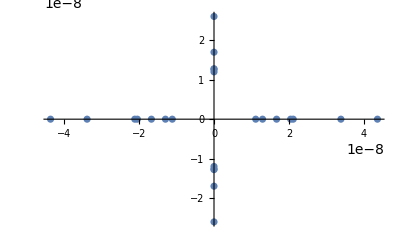

```mathematica
ListPlot[ReIm[Chop[Sort[Join[λs,λs]]-Sort[Bigλs,Re[#1]≤Re[#2]&]]]]
```

```mathematica
{-4.841675260090206,-4.138738037874365,4.123013324295264,-3.1656927617265747,3.1197169785363426,-2.7857563549514497,2.5748261672286707,-1.508610381998243,1.0278863770970044,0.3919086457591809,-0.3310837955674989,-0.19466087035822985}
```

```mathematica
{-4.841675326624646+0. ⅈ,
-4.841675193555767+0. ⅈ,
-4.138738037874356+6.764554388012403*^-8 ⅈ,-4.138738037874356-6.764554388012403*^-8 ⅈ,4.1230133242952665+4.556433849775215*^-8 ⅈ,4.1230133242952665-4.556433849775215*^-8 ⅈ,-3.1656927617265755+5.822856575535849*^-9 ⅈ,-3.1656927617265755-5.822856575535849*^-9 ⅈ,3.119716978536342+1.3271208457798974*^-8 ⅈ,3.119716978536342-1.3271208457798974*^-8 ⅈ,-2.785756399263059+0. ⅈ,-2.785756310639844+0. ⅈ,2.5748261672286707+3.04235976747412*^-8 ⅈ,2.5748261672286707-3.04235976747412*^-8 ⅈ,-1.5086103819982446+1.8266999920110067*^-8 ⅈ,-1.5086103819982446-1.8266999920110067*^-8 ⅈ,1.0278863945843784+0. ⅈ,1.027886359609633+0. ⅈ,0.39190864575918083+2.2810390096194057*^-8 ⅈ,0.39190864575918083-2.2810390096194057*^-8 ⅈ,-0.33108381029441586+0. ⅈ,-0.3310837808405815+0. ⅈ,-0.19466088105273122+0. ⅈ,-0.1946608596637286+0. ⅈ}
```

Bigλs